# Problem 1/2

```mathematica
EquilateralTriangle[s_]:=SSSTriangle[s,s,s];
Graphics[{EdgeForm[Directive[Thick,Black]],Opacity[0],EquilateralTriangle[1]}]
```

-Graphics-

```mathematica
α=0;
b=Graphics3D[{Opacity[α],Cube[{0,0,0}],Opacity[α],Cube[{1,1,0}],Opacity[1],Thick,Red,Line[{{1.5,1.5,0.5},{0.5,0.5,-0.5},{-0.5,-0.5,0.5}}]},ViewAngle->Pi/7,Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\tetrahedral.png",b]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\tetrahedral.png

```mathematica
b
```

-Graphics3D-

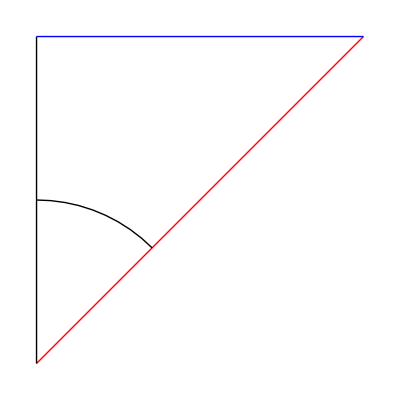

```mathematica
a=Graphics[{Thick,Red,Line[{{0,0},{1,1}}],Thin,Black,Line[{{0,1},{0,0}}],Thick,Blue,Line[{{1,1},{0,1}}],Black,Circle[{0,0},0.5,{Pi/4,Pi/2}]}]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\triangle1.png",a]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\triangle1.png

```mathematica
N@(2*ArcCos[1/(√3)]*180/Pi)
```

109.471

```mathematica
Dot[{1,1,-1},{2,2,0}]/(Length[{1,1,-1}]*Length[{2,2,0}])
```

4/9

```mathematica
ParallelQ
```

```mathematica
MatrixRank[{{1,1,-1},{2,2,0}}]==1
```

False

```mathematica
Integrate[x^2,{x,0,4/3}]
```

64/81

```mathematica
Integrate[x,{x,0,4/3}]^2
```

64/81

```mathematica
N@120°
```

2.0944

```mathematica
π Rationalize[N[2.0943951023931953]/π]
```

(2 π)/3

# Problem 3

```mathematica
hexagon[z_]:=
Module[{r,n,pts,newv},
r=RotationMatrix[π/3,{0,0,1}];
n=1;
pts={{{0},{1},{z}},{},{},{},{},{}};
Do[ newv=pts[[n]];
pts[[n+1]]=r.newv;
n++,5];
Append[Partition[Flatten[pts],3],{0,0,z}]
]
triangle[z_]:=
Module[{r,n,pts,newv},
r=RotationMatrix[120°,{0,0,1}];
n=1;
pts={RotationMatrix[30°,{0,0,1}].{{1/2},{1/(2 √3)},{z}},{},{}};
Do[ newv=pts[[n]];
pts[[n+1]]=r.newv;
n++,2];
Partition[Flatten[pts],3]
]
triangle2:=
Module[{r,n,pts,newv},
r=RotationMatrix[120°];
n=1;
pts={{{0},{1}},{},{}};
Do[ newv=pts[[n]];
pts[[n+1]]=r.newv;
n++,2];
Partition[Flatten[pts],2]
]
```

```mathematica
h1=hexagon[0]; (*Create the hexagon on the bottom*)
h2=hexagon[1.5]; (*Create the top hexagon*)
t=triangle[0.75];
x=Graphics3D[{PointSize[0.1],Red,Point[h1],Point[h2],Green,Point[t]},
Axes->True,Ticks->None,Boxed->False,
ViewVertical->{0,0,1},ViewAngle->Pi/8]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\hcp1.png",x]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\hcp1.png

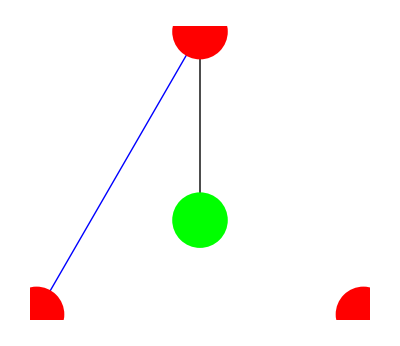

```mathematica
img1=Graphics[{
Thick,Black,Line[{{1/2,1/(2 √3)},{1/2,(√3)/2}}],
Thick,Blue,Line[{{0,0},{1/2,(√3)/2}}],
PointSize->0.1,Red,Point[{{0,0},{1,0},{1/2,(√3)/2}}],
Green,Point[RegionCentroid[Region@SSSTriangle[1,1,1]]]}]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\hcp2.png",img1]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\hcp2.png

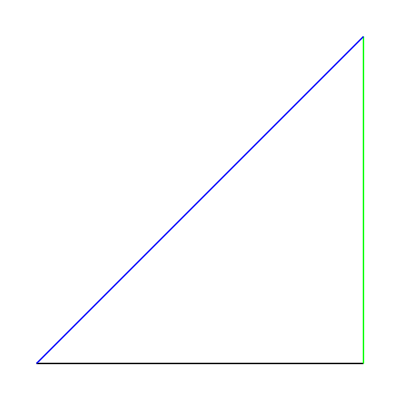

```mathematica
img2=Graphics[{
Thick,Black,Line[{{0,0},{1,0}}],
Thick, Green,Line[{{1,0},{1,1}}],
Thick,Blue,Line[{{1,1},{0,0}}]
}]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\hcp3.png",img2]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\hcp3.png

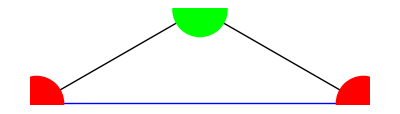

```mathematica
img3=Graphics[{
Thick,Black,Line[{{1/2,1/(2 √3)},{0,0}}],
Thick,Black,Line[{{1/2,1/(2 √3)},{1,0}}],
Thick,Blue,Line[{{0,0},{1,0}}],
PointSize->0.1,Red,Point[{{0,0},{1,0}}],
Green,Point[RegionCentroid[Region@SSSTriangle[1,1,1]]]}]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\hcp4.png",img3]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\hcp4.png

```mathematica
Sin[30°]/Sin[120°]
```

1/(√3)

# Problem 4

Generalized form of hexagon and triangle functions from above in 2d and 3d

```mathematica
genShape3D[nPts_,z_]:=
Module[{r,n,pts,newv},
r=RotationMatrix[2π/nPts,{0,0,1}];
n=1;
pts={{{0},{1},{z}}};
Do[ newv=pts[[n]];
pts = Append[pts,r.newv];
n++,nPts-1];
Partition[Flatten[pts],3]
]
genShape2D[nPts_]:=
Module[{r,n,pts,newv},
r=RotationMatrix[2π/nPts];
n=1;
pts={{{0},{1}}};
Do[ newv=pts[[n]];
pts = Append[pts,r.newv];
n++,nPts-1];
Partition[Flatten[pts],2]
]
```

0.3

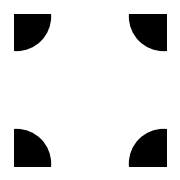

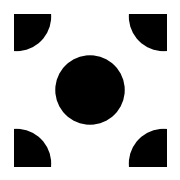

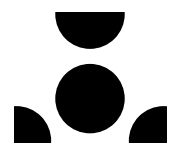

```mathematica
ptsize=0.3
bcc100=Graphics[{PointSize->ptsize,Point@{{0,0},{0,1},{1,1},{1,0}},
EdgeForm[Directive[Thick,Black]],Opacity[0],Rectangle[{0,0}]},
ImageSize->Small]
bcc110=Graphics[{PointSize->ptsize,Point@{{0,0},{0,1},{1,1},{1,0}},
Point@RegionCentroid@ConvexHullMesh@{{0,0},{0,1},{1,1},{1,0}},
EdgeForm[Directive[Thick,Black]],Opacity[0],Rectangle[{0,0}]},

ImageSize->Small]
bcc111=Graphics[{PointSize->ptsize,Point@genShape2D[3],Point@RegionCentroid@ConvexHullMesh@genShape2D[3],
EdgeForm[Directive[Thick,Black]],Opacity[0],Triangle[genShape2D[3]]},
ImageSize->Small]
```

```mathematica
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\bcc100.png",bcc100]
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\bcc110.png",bcc110]
Export["C:\\Users\\mcard\\Documents\\school-dir\\SP22\\PHYS437\\figs\\bcc111.png",bcc111]
```

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\bcc100.png

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\bcc110.png

C:\Users\mcard\Documents\school-dir\SP22\PHYS437\figs\bcc111.png

```mathematica
genShape2D[4]
```

{{0,1},{-1,0},{0,-1},{1,0}}

```mathematica
Area[SSSTriangle[a,a,a]]
```

1/4 √3 Abs[a]^2

```mathematica
(3/2 π a^2 3/16)/(a^2(√3)/2)
```

(3 √3 π)/16

# Problem 5

```mathematica
ElementData["Aluminum","LatticeConstants"]
```

{404.95 pm,404.95 pm,404.95 pm}

```mathematica
Quantity[404.95`5., "Picometers"]
```

404.95 pm

```mathematica
UnitConvert[Quantity[404.95`5.,"Picometers"],"Angstroms"]
```

4.0495 Å

```mathematica
UnitConvert[Quantity[4.0495`5.,"Angstroms"],"cm"]
```

4.0495×10^-8 cm

```mathematica
4/((4.0495*10^-8)^3)
```

6.0236×10^22

# Problem 6